# Reaction diffusion systems

## Jovana Andrejevic, Nina Andrejevic, Amina Matt, and George Varnavides

### Alan Turing suggested first that morphogenesis could be modeled as a reaction-diffusion mechanism.

#### Other application in chemistry, physiology (heart and brain), plant

### Pattern in biological systems

```mathematica
-Graphics--Graphics-
```

J.D.Murray, How the leopard gets its spots.Sci.Am.258, 80–87 (1988).
A.J.Koch, H.Meinhardt, Biological pattern formation : from basic mechanisms to complex structures.Rev.Mod.Phys.66, 1481–1507 (1994).

## Chemistry

### Belousov - Zhabotinsky (BZ) reaction : a 17 years effort

The BZ reaction was the first nonlinear chemical oscillator found, i.e. the colour of the solution was oscillating between a colourless and a yellow solution. Boris Belousov, in 1951, tried to publish his results twice but his explanation didn’t satisfy the reviewers. Indeed, it was believed that the reaction violated the second law of thermodynamics. ΔS≥0. The paradox was solved when it was shown that the reaction happened far from equilibrium. 

He published later on in a less-known journal. A PhD student, Zhabotinsky, took on the project later one and was finally able to share the results in 1968!

https : // commons.wikimedia.org/wiki/File : Bzr_raum.jpg

## Physiology

#### Heart arrhythmia is controlled by electrical activity. The electrical waves that control the rhythmic muscle contraction can be related to some specific pattern. In the worst case a singularity can stabilize a life-threatening heart arrhythmia.

## Vegetation

#### Patterns also occur at large length-scale and over long timescale.

P.Gandhi, L.Werner, S.Iams, K.Gowda, M.Silber, A topographic mechanism for arcing of dryland vegetation bands.J.Royal Soc.Interface.15, 20180508 (2018).

# Gray-Scott model of reaction diffusion

```mathematica
-Graphics--Graphics-
```

Complex Patterns in a Simple System, John E. Pearson, Science, New Series, Vol. 261, No. 5118 (Jul. 9, 1993), pp. 189-192 Published by: American Association for the Advancement of Science Stable  https://www.jstor.org/stable/2881810

Nonlinear dynamics and chaos, with application to Physics, Biology, Chemistry, and Engineering,  S.H.Strogatz, Second Edition, Westwiew Press.

## Gray-Scott model

### The chemical reactions are the following -Graphics-

Comments:
	- reactions are irreversible
	- P is an inert product

U is red. V is blue.

### The system of PDE’s describing the reaction is the following -Graphics-

where u and v are the concentration of chemical species, D_uand D_v are the diffusion coefficients. 
F is the dimensionless feed rate of U and k is the dimensionless rate constant of the second reaction.

#### Diffusion term

The diffusion process is proportional to the diffusion coefficient as well as the Laplacian, i.e. local variation of the gradient.

#### Reaction term

The reaction requires one U and two V: the rate is proportional to U^1and V^2.  As U is converted in V , (i.e. U is used and V is produced) the sign are - and + respectively in equation of U and V.

#### Feed and kill term

F is the feed term, i.e. rate at which U is added to the system (if not there is a point where U is completely used up). 
For U equation, the feeding term is proportional to the difference between the maximal concentration and the actual concentration: (1-U). Thus even without diffusion and reaction the concentration of F cannot exceed 1 (also called (which describe better its role, in my opinion) the replenishment term). If you want to go further in interpretation: In a real system it would be a membrane with permeability F, that diffuse proportionally to (1-U). The feeding term is always >0.

k is the killing term, i.e. rate at which V is removed from the system (through the second reaction V → P).  V is produced and remove at a killing rate k, but also it diffuses out through the same process as U is fed, thus -FV and -kV. Again a further interpretation is that the same membrane enclosed the entire system.

## Spectral method to solve the system of PDE' s

```mathematica
recomputeSpectralTerms[{nx_Integer, ny_Integer}]:= Module[{kx,ky,kmags2,kvec},
kvec[nSize_] := Module[{baseVec},
baseVec = Range[-(1+1/nSize),1,2/nSize];  (*setting up the k-vector*)
If[EvenQ[nSize],
baseVec = Range[-1,1/1,2/nSize];
baseVec = Rest[baseVec];
baseVec = RotateLeft[baseVec,nSize/2 -1], (*n=then odd*)
baseVec = Range[-(1+ 1/nSize),1+ 1/nSize,2/nSize];
baseVec = Most[Rest[baseVec]];
baseVec = RotateLeft[baseVec,(nSize-1)/2]
];
N[Pi] baseVec
];

kx = nx Transpose[ConstantArray[kvec[nx],ny]];
ky = ny ConstantArray[kvec[ny],nx];
 
kmags2 = kx^2 + ky^2;

goForwardDiffusion2D[c_, diffC_,  dt_]:=
Re@InverseFourier[Fourier[c]/(1 + diffC*dt*kmags2)]; (*the n^2 is now captured in the k matrix*)

(*-----------------*)
goForwardGrayScott[{u_, v_}, {diffU_, diffV_,f_, k_},  dt_]:=
Block[
{fourierU = Fourier[u], 
fourierV =  Fourier[v],
uvSquared  = u v^2, 
fourieruvSquared,
fourierVDriving
},
fourieruvSquared = Fourier[ u v^2];

{
Re@InverseFourier[(fourierU +  dt(Fourier[f(1-u)] - fourieruvSquared))/(1 + diffU*dt*kmags2)],
Re@InverseFourier[(fourierV + dt(fourieruvSquared-Fourier[(f+ k)v]))/(1 + diffV*dt*kmags2)]
}
];
 
]
```

## The solutions : oscillatory or not

```mathematica
uEq=(0 == (rhsU = ϕ (1 - u) - u v^2));
vEq=(0 == (rhsV =  -(ϕ +k)v + u v^2));
```

```mathematica
solUV=Simplify[Solve[{uEq,vEq},{u,v}],Assumptions -> (*k>0 && ϕ> 0 && *)ϕ  ∈ Reals && k ∈ Reals]
```

{{u→1,v→0},{u→(ϕ+√(-ϕ (4 k^2+8 k ϕ+ϕ (-1+4 ϕ))))/(2 ϕ),v→(ϕ-√(ϕ (ϕ-4 (k+ϕ)^2)))/(2 (k+ϕ))},{u→(ϕ-√(-ϕ (4 k^2+8 k ϕ+ϕ (-1+4 ϕ))))/(2 ϕ),v→(ϕ+√(ϕ (ϕ-4 (k+ϕ)^2)))/(2 (k+ϕ))}}

### With a linear stability analysis and the Poincare-Bendixson theorem the parameters corresponding to the oscillatory solutions can be found. We won’t go through this part but will use the suitable parameters. F = 0.005 and k=0.026

## Visualization for a system with periodic boundary conditions.

```mathematica
initialize:=
Module[{},
uValuesImage=Image[Graphics[MapThread[{GrayLevel[#1],Disk[#2]}&,{RandomReal[{0.3,0.7},8],RandomReal[{0,10},{8,2}]}],Background-> White],ColorSpace-> "Grayscale",ImageSize->{256,256}];
vValuesImage=Image[Graphics[MapThread[{GrayLevel[#1],Disk[#2]}&,{RandomReal[{0.1,0.5},8],RandomReal[{0,10},{8,2}]}],Background-> Black],ColorSpace-> "Grayscale",ImageSize->{256,256}];
uValues=ImageData[uValuesImage];vValues=ImageData[vValuesImage];
recomputeSpectralTerms[Dimensions@uValues];
]
```

#### Set some initial concentration of chemical species u and v.

```mathematica
initialize
```

```mathematica
Grid[{{uValuesImage,vValuesImage}}]
```

-Graphics- | -Graphics-

#### Create a function that will solve each iteration.

```mathematica
run[F_,k_]:=Do[
{uValues,vValues}=goForwardGrayScott[{uValues,vValues},{2*10^-6,1*10^-6,F,k},2];
uValuesList=AppendTo[uValuesList,uValues];
,
{3000}
]
```

## Visualization I : Periodic boundary condition and oscillation

```mathematica
uValuesList={};
```

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"Rainbow",ColorFunctionScaling->False],ImageSize->Large]]*)
initialize
run[0.005,0.026]
```

```mathematica
im=Image[Raster[uValuesList[[100]],ColorFunction->"Rainbow",ColorFunctionScaling->False],ImageSize->Large]
```

#### Movie : 1_Oscillating_PBC_GS_System

## Visualization II

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"NeonColors",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
(*Dynamic[Image[Raster[vValues,ColorFunction->"GreenPinkTones",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
initialize
```

```mathematica
run[0.005,0.026]
```

#### Movie : 2_Oscillating_PBC_GS_System_GreenPink

#### Movie : 2_Oscillating_PBC_GS_System_Neon

## Visualization III : let’s try to seed with something else

```mathematica
kaa=Import["/Users/aminamatt/Dropbox/Generative-Art_2020/Thursday/Scratch/targetOscillation.jpg"]
```

-Graphics-

```mathematica
uValuesImageKaa=ImageRotate[ImageRotate[
ImageResize[
ColorConvert[kaa, "Grayscale"],
{256,256}],Left],Left]
```

-Graphics-

```mathematica
vValuesImageKaa=ImageResize[ColorConvert[Graphics[{GrayLevel[0.1],Rectangle[]}],"Grayscale"],{256,256}]
```

-Graphics-

```mathematica
initializeII:=
Module[{},
uValues=ImageData[uValuesImageKaa];vValues=ImageData[vValuesImageKaa];
recomputeSpectralTerms[Dimensions@uValues];
]
```

```mathematica
runII[F_,k_]:=Do[
{uValues,vValues}=goForwardGrayScott[{uValues,vValues},{2*10^-6,1*10^-6,F,k},0.5];
uValuesList=AppendTo[uValuesList,uValues];
,
{3000}
]
```

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"Rainbow",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
initializeII
```

```mathematica
runII[0.005,0.026]
```

#### Movie : 3_Oscillating_GS_System_Kaa

## Non oscillatory pattern : Stripes and dots

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"CherryTones",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
initialize
```

```mathematica
run[0.024,0.056](*stripes and dots*)
```

#### Movie : 4_Dots_PBC_GS_System_CherryTones

## Non oscillatory pattern : Dots

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"CherryTones",ColorFunctionScaling->False],ImageSize->Medium]]*)
```

```mathematica
(*uValuesReduced=Table[uValuesList[[10 i]],{i,1,500}];*)
```

```mathematica
(*uValuesImage=Image[Raster[#,ColorFunction->"CherryTones",ColorFunctionScaling->False],ImageSize->Large]&/@uValuesReduced*)
```

```mathematica
initialize
```

```mathematica
run[0.024,0.06](*dots*)
```

$Aborted

#### Movie : 4_DotsStripes_PBC_GS_System_CherryTones

## Non oscillatory pattern : Hexagon

```mathematica
(*Dynamic[Image[Raster[uValues,ColorFunction->"GrayTones",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
initialize
```

```mathematica
run[0.032,0.056](*hexagon*)
```

#### Movie : 4_hexagon_PBC_GS_System_GrayTones

## Length scale

```mathematica
initializeLengthScale[nCircles_]:=Module[{},
uValuesImage=Image[Graphics[MapThread[{GrayLevel[#1],Disk[#2]}&,{RandomReal[{0.3,0.7},nCircles],RandomReal[{0,25},{nCircles,2}]}],Background-> White],ColorSpace-> "Grayscale",ImageSize->{256,256}];
vValuesImage=Image[Graphics[MapThread[{GrayLevel[#1],Disk[#2]}&,{RandomReal[{0.1,0.5},nCircles],RandomReal[{0,25},{nCircles,2}]}],Background-> Black],ColorSpace-> "Grayscale",ImageSize->{256,256}];
uValues=ImageData[uValuesImage];vValues=ImageData[vValuesImage];
recomputeSpectralTerms[Dimensions@uValues];
]
```

```mathematica
(*Dynamic[Image[Raster[vValues,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],ImageSize->Large]]*)
```

```mathematica
uValuesImage=Image[Raster[#,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],ImageSize->Large]&/@uValuesList;
```

```mathematica
initializeLengthScale[1]
```

```mathematica
run[0.032,0.056](*hexagon*)
```

#### Movie : 5_hexagon_PBC_GS_System_TemperatureMap

### From this last simulation we can think about playing with the boundary conditions.

# Non periodic boundary conditions

#### In this case the spectral method isn’t adapted and a numerical implementation with finite element is used. (see Wolfram demonstrations)

### Equations

```mathematica
eqn = {
    Derivative[1,0,0][u][t, x, y] + 
      Inactive[Div][(-c1 Inactive[Grad][u[t, x, y], {x, y}]), {x, y}] +
      (v[t, x, y]^2 + f) u[t, x, y] == f, 
    Derivative[1,0,0][v][t, x, y] + 
      Inactive[Div][(-c2 Inactive[Grad][v[t, x, y], {x, y}]), {x, y}] +
      (-u[t, x, y] v[t, x, y] + f + k) v[t, x, y] == 0
    } ;
```

### Initial condition

```mathematica
ics={
u[0,x,y]==1/2,
v[0,x,y]==If[x^2+y^2≤1/40,1,0]};
```

### Dirichlet boundary conditions

```mathematica
bcs=DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},True];
```

### Domain

```mathematica
domain=Disk[]
```

Disk[{0,0}]

### Finite element

```mathematica
{ufun,vfun}=
NDSolveValue[{eqn//. {c1 -> 2*10^-5, c2 -> c1/4, f -> 1/25, k -> 3/50},bcs,ics},{u,v},{x,y}∈domain,{t,0,3000},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.003}}}}];(*Only on version 12*)
{vmin,vmax}=MinMax[vfun["ValuesOnGrid"]];
```

$Aborted

```mathematica
?NDSolveValue
```

### Visualization

```mathematica
frames=
Table[
ContourPlot[vfun[t,x,y],{x,-1,1},{y,-1,1},Sequence[Contours->Range[vmin,vmax,(vmax-vmin)/4],PlotRange->All,Frame->None,Axes->None,ColorFunction-> Hue]],{t,10,2000,25}];
```

```mathematica
(*Export["Name", frames]*)
```

```mathematica
(*Import["","Animation"]*)
```

#### Movie : 6_DirichletBC _GS

### Another visualisation

```mathematica
domain=Rectangle[{-1,-1},{1,1}]
```

Rectangle[{-1,-1},{1,1}]

```mathematica
{ufun,vfun}=
NDSolveValue[{eqn//. {c1 -> 2*10^-5, c2 -> c1/4, f -> 1/25, k -> 3/50},bcs,ics},{u,v},{x,y}∈domain,{t,0,1000},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.003}}}}];
{vmin,vmax}=MinMax[vfun["ValuesOnGrid"]];
```

```mathematica
frames=Table[ContourPlot[vfun[t,x,y],{x,-1,1},{y,-1,1},Sequence[Contours->Range[vmin,vmax,(vmax-vmin)/4],PlotRange->All,PlotRangePadding-> 0,ImagePadding-> 0, ImageMargins->0, Frame->None,Axes->None,ColorFunction-> Hue]],{t,1,100,25}];
```

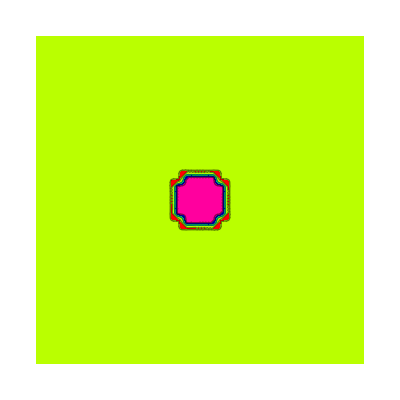
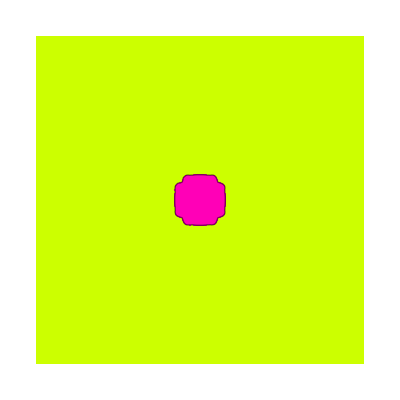
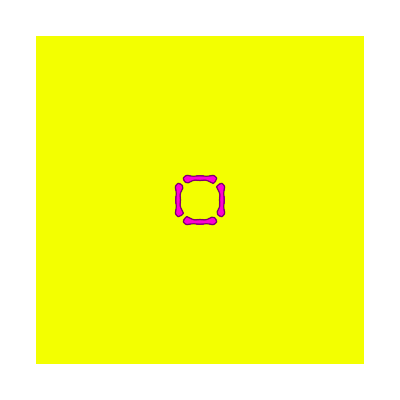
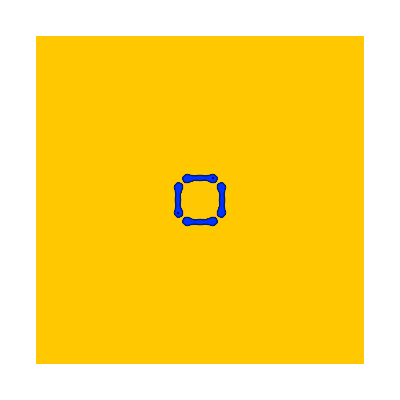

```mathematica
frames[[1;;4]]
```

#### Movie : 6_Dirichlet_Rectangle_GS

# On a torus

## Another way to use these results on a surface embedded in 3D space is to map the results of a square onto a torus.

## A torus can be formed from a 2 D sheet.

```mathematica
(*Code from matehmatica stack exchange Kuba *)DynamicModule[{x=2.,l=100.,x2=2.,l2=100.(*,grid,fast,slow*)},Grid[{{Graphics3D[{Dynamic[Map[{Blue,Polygon[#[[{1,2,4,3}]]]}&,Join@@@(Join@@Partition[#,{2,2},1])]&[ControlActive[fast[l,l2],slow[l,l2]]]]},PlotRange->{{-7,7},{-7,7},{-1,2}},ImageSize->600,Axes->True,BaseStyle->18],Column[{Slider[Dynamic[x,(l=10.^#;x=#)&],{.0001,2.}],Slider[Dynamic[x2,(l2=10.^#;x2=#)&],{.0001,2.}]}]}}],
Initialization:>(grid[l_,l2_,n_,m_]:=
Outer[
Compose,
(**)Array[RotationTransform[# Pi/l2,{0,0,1.},{0,-l2,0}]&,n,{-1,1}],
(**)Array[RotationTransform[# Pi/l,{1.,0,0},{0,2,l}][{0,2,0}]&,m,{-1,1}],1];
fast[l_,l2_]=grid[l,l2,10,10];
slow[l_,l2_]=grid[l,l2,50,25];)]
```

```mathematica
ParametricPlot3D[{(2+Cos[2 Pi v]) Cos[2 Pi u],(2+Cos[2 Pi v]) Sin[2 Pi u],Sin[2 Pi v]},{u,0,1},{v,0,1}]
```

```mathematica
torusFrames=ParametricPlot3D[{(2+Cos[2 Pi v]) Cos[2 Pi u],(2+Cos[2 Pi v]) Sin[2 Pi u],Sin[2 Pi v]},{u,0,1},{v,0,1},PlotStyle->{Lighting-> "Neutral",Texture[frames[[#]]]},PlotPoints->100,Mesh->None,Axes->None]&/@Table[t,{t,1,4,1}];
```

```mathematica
Manipulate[
ParametricPlot3D[{(2+Cos[2 Pi v]) Cos[2 Pi u],(2+Cos[2 Pi v]) Sin[2 Pi u],Sin[2 Pi v]},{u,0,1},{v,0,1},PlotStyle->{Lighting-> "Neutral",Texture[frames[[t]]]},PlotPoints->100,Mesh->None,Axes->None],{t,1,4,1}]
```

#### Movie: 7 _Torus _GS

# The 3D picture

```mathematica
frames[[1;;5]]
```

```mathematica
Dimensions@frames
```

{120}

```mathematica
Plot3D[vfun[50,x,y],{x,-1,1},{y,-1,1},PlotRange->All,MaxRecursion->4,PlotPoints->25,ColorFunction->Hue]
```

```mathematica
landscape3D=Table[Plot3D[vfun[t,x,y],{x,-1,1},{y,-1,1},PlotRange->All,MaxRecursion->4,PlotPoints->25,ColorFunction->Hue],{t,{50,2000,2500,3000}}];
```

```mathematica
landscape3D[[1]]
```

```mathematica
Show[landscape3D[[3]],ImageSize->Large]
```